# Super Shapes

## Super Ellipse in 2D

### x^2 + y^2 = r^2 x = r * cos(o) y = r * sin(o)

```mathematica
r = 100;
```

```mathematica
Table[Point[{r * Cos[a],r * Sin[a]}],{a,2 Pi}]
```

{Point[{100 Cos[1],100 Sin[1]}],Point[{100 Cos[2],100 Sin[2]}],Point[{100 Cos[3],100 Sin[3]}],Point[{100 Cos[4],100 Sin[4]}],Point[{100 Cos[5],100 Sin[5]}],Point[{100 Cos[6],100 Sin[6]}]}

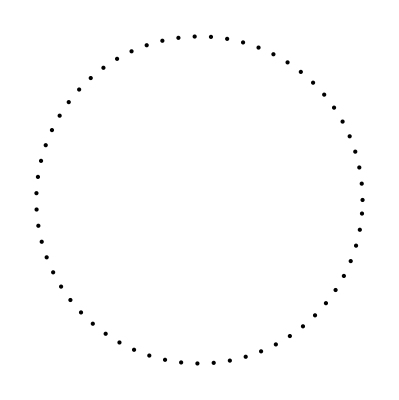

```mathematica
Graphics[Table[Point[{r * Cos[a],r * Sin[a]}],{a,0,2 Pi,0.1}]]
```

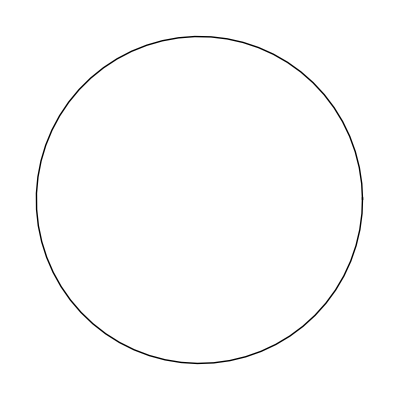

```mathematica
Graphics[Line[{Table[{r * Cos[a],r * Sin[a]},{a,0,2 Pi+0.1,0.1}]}]]
```

### |x/a|^n+|Y/b|^n = 1 a = r, b = r, n =2 x^2 + y^2 = r^2 x(o) = |cos o|^2/n * a sgn(cos o) y(o) = |sin o|^2n * b sgn(sin o)

```mathematica
sgn[val_] :=  If[val>0,1,-1,0];
```

x = Power[Abs[Cos[angle]], na] * a * sgn[Cos[angle]];
y = Power[Abs[Sin[angle]], na] * b * sgn[Sin[angle]];

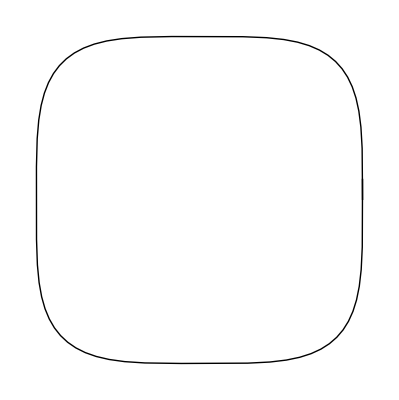

```mathematica
a = 100;
b = 100;
n = 4;
na = 2 / n;
Graphics[
Line[
{Table[
{Power[Abs[Cos[angle]],na] * a * sgn[Cos[angle]],Power[Abs[Sin[angle]],na] * b * sgn[Sin[angle]]},{angle,0,2 Pi+0.1,0.1}
]}
]
]
```

```mathematica
a = 100;
b = 100;
Animate[
Graphics[
Line[
{Table[
{Power[Abs[Cos[angle]],2/n] * a * sgn[Cos[angle]],Power[Abs[Sin[angle]],2/n] * b * sgn[Sin[angle]]},{angle,0,2 Pi+0.1,0.1}
]}
]
],{n,0.5,4,.1},AnimationRunning->False,DefaultDuration->2]
```

## Super Shapes in 2D

### 1/r = n1 SequareRoot[|1/a cos(m/4 o)|^n2 + |1/b sin(m/4 0)|^n3]

```mathematica
$a = 1;
$b = 1;
superShape[theta_,m_,n1_,n2_,n3_] := 
	Module[{thet = theta},
		part1 = Power[Abs[(1 / a) * Cos[thet * m / 4]],n2];
		part2 = Power[Abs[(1 / b) * Sin[thet * m / 4]],n3];
		part3 = Power[part1 + part2, 1 / n1];
		If[part3 == 0, 0, 1/part3]
	]
```

```mathematica
radius = 100;
totalPoints = 1000;
increment = 2 Pi / totalPoints;
Manipulate[Graphics[
Line[
{Table[
{radius * superShape[angle,m,n1,n2,n3] *Cos[angle],
radius * superShape[angle,m,n1,n2,n3] *Sin[angle]},
{angle,0,2 Pi ,increment}
]}
]
],{m,0,10,1},{n1,1,60,1},{n2,1,60,1},{n3,1,60,1}]
```

## Super Shapes in 3D

```mathematica
Graphics3D[
      Table[Point[{r * Sin[lat]*Cos[lon], r * Sin[lat]*Sin[lon], r*Cos[lat]}],
          {lat, -Pi, Pi + 1, 0.2}, {lon, -2 Pi, 2 Pi + 1, 0.2}]
      ]
```

-Graphics3D-

```mathematica
map[n_, start1_,stop1_,start2_,stop2_] := ((n-start1)/(stop1-start1))*(stop2-start2)+start2
ClearAll[createPoints]
ClearAll[createTriangles]
```

```mathematica
$a = 1;
$b = 1;
supershape[thate_,m_,n1_,n2_,n3_] := 
Module[{t1,t2,t3},
	t1 = Power[Abs[(1/a)*Cos[m * thate / 4]],n2];
	t2 = Power[Abs[(1/b)*Sin[m * thate / 4]],n3];
	t3 = t1 +  t2;
	Power[t3,-1/n1]
];
createPoints[total_:100, r_:200] := 
Table[
	With[{
	lat = map[i,0, total,-Pi/2, Pi/2],
	lon = map[j,0, total, -Pi, Pi]
	},With[{
	r1 = supershape[lon,7,0.2,1.7,1.7],
	r2 = supershape[lat,7,0.2,1.7,1.7]},
	{r*r1*Cos[lon]*r2*Cos[lat],r*r1*Sin[lon]*r2*Cos[lat],r*r2*Sin[lat]}]
	], 
	{i, 1, total+1}, 
	{j, 1, total+1}
]
```

```mathematica
createTriangles[{p1_,p2_},{p3_,p4_}] := {Triangle[{p1,p3,p4}],Triangle[{p1,p2,p4}]}
applyGraphics[] := Graphics3D@Flatten[Apply[createTriangles,Partition[N@createPoints[100,200],{2,2},1],{2}]]
```

### Examples :

SuperShape 1 : m = 7, n1 = 0.2, n2 = 1.7, n3 = 1.7
SuperShape 1 : m = 7, n1 = 0.2, n2 = 1.7, n3 = 1.7

```mathematica
applyGraphics[]
```

-Graphics3D-

SuperShape 1: m = 8, n1 = 60, n2 = 100, n3 = 20
SuperShape 1: m = 2, n1 = 10, n2 = 10, n3 = 10

```mathematica
applyGraphics[]
```

-Graphics3D-

SuperShape 1: m = 2, n1 = 0.7, n2 = 0.3, n3 = 0.2
SuperShape 1: m = 3, n1 = 100, n2 = 100, n3 = 100

```mathematica
applyGraphics[]
```

-Graphics3D-